```mathematica
p[z_]=(z^2-1)(z-λ); lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z]; soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z];
r0=1.;r1=-1.;r2=λ;
rootPosition := Compile[{{z,_Complex}},
    Which[Abs[z -r0] <  10.0^(-6),3,
Abs[z-r1]<10.0^(-6), 2,
Abs[z-r2]<10.0^(-6), 1,
    True, 0],
{{rootf[_],_Complex}}
]
iterSchLambda = Compile[{{z, _Complex},{ λ,_Complex}},(4 z^3+λ-10 z^2 λ+z^4 λ+4 z λ^2)/(1+3 z^4-4 z λ-4 z^3 λ+2 λ^2+2 z^2 λ^2)];
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
    Block[{z,λ,ct,r}, z =z/.soluciones[[3]];
λ= x + y I; ct = 0;r = rootPosition[z];
raiz1=0;
        While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
	If[r==0,Return[N[0]],raiz1=N[r]];	    

		  
z =z/.soluciones[[2]];λ= x + y I; ct = 0;r = rootPosition[z];
     raiz2=0   ;
While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
	If[r==0,Return[N[0]],raiz2=N[r]];	    

z =z/.soluciones[[1]];λ= x + y I; ct = 0;r = rootPosition[z];
     raiz3=0;  
 While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
	If[r==0,Return[N[0]],raiz3=N[r]];	    

	Return[N[(raiz3-1)*9+(raiz2-1)*3+raiz1]](*Devuelve un numero del 1 al 27 que marcará el color*)

    ]
Clear[fractalColorWS]
fractalColorWS[p_] :=
Switch[IntegerPart[p],
28, RGBColor[1,1,1],
0, Black,
1,Hue[0.036],
2,Hue[0.072],
3,Hue[0.10799999999999998],
4,Hue[0.144],5,Hue[0.18],
6,Hue[0.21599999999999997],
7,Hue[0.252],8,Hue[0.288],
9,Hue[0.32399999999999995],
10,Hue[0.36],
11,Hue[0.39599999999999996],
12,Hue[0.43199999999999994],
13,Hue[0.46799999999999997],
14,Hue[0.504],
15,Hue[0.5399999999999999],
16,Hue[0.576],
17,Hue[0.612],
18,Hue[0.6479999999999999],
19,Hue[0.6839999999999999],
20,Hue[0.72],
21,Hue[0.7559999999999999],
22,Hue[0.7919999999999999],
23,Hue[0.828],
24,Hue[0.8639999999999999],
25,Hue[0.8999999999999999],
26,Hue[0.9359999999999999],
27,White


]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
Clear[plotColorFractal]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,29},(* Three roots + fixed  *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
Off[General::ovfl];    Off[General::unfl];    Off[Infinity::indet]
Off[CompiledFunction::cccx];    Off[CompiledFunction::cfn]; Off[CompiledFunction::cfcx];    Off[CompiledFunction::cfex]; Off[CompiledFunction::crcx];    Off[CompiledFunction::cfse]; Off[CompiledFunction::ilsm];    Off[CompiledFunction::cfsa]
```

```mathematica
numberPoints =512;limIterations=100;
xxMin=-5.25; xxMax=5.25; yyMin=-3.4; yyMax=3.4;plotColorFractal[iterSchLambda, numberPoints]
```

```mathematica
numberPoints =1024;limIterations=100;
xxMin=-0.0125; xxMax=0.0125; yyMin=1.7215; yyMax=1.74125;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

```mathematica
numberPoints =1024;limIterations=100;
xxMin=-0.0125/4; xxMax=0.0125/4; yyMin=1.73137-(1.74125-1.7215)/4; yyMax=1.73137+(1.74125-1.7215)/4;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

```mathematica
numberPoints =1024;limIterations=100;
xxMin=-500; xxMax=500; yyMin=-500; yyMax=500;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

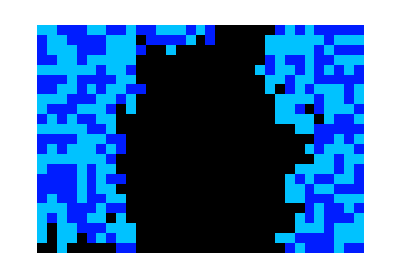

```mathematica
numberPoints =32;limIterations=400;
xxMin=3.619; xxMax=3.627; yyMin=143.095; yyMax=143.1;plotColorFractal[iterSchLambda, numberPoints]
```